```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Diamonds*)ClearAll[etaCYL3,F,R,GAMMAperp,GAMMAone];
GAMMAperp[x_]=(2/x^2) (1-Exp[-x^2]*(BesselI[0,x^2]+BesselI[1,x^2]));
GAMMAone[y_]=(2/y^2) (Exp[-y^2]-1+Sqrt[Pi/2]*y*Erf[y/Sqrt[2]]);
etaCYL3[rc_]=(((2*dens*(Pi (R^2)*d))^2)/(d^2)) GAMMAperp[((R)/(Sqrt[2]*rc))] (1-Exp[(-d^2)/(4 rc^2)]);
LamCYL[rc_]=1/(4 etaCYL3[rc] (Δx)^2 t);
F[rc_,lambda_]=lambda (4 etaCYL3[rc] (Δx)^2 t)-1;
R=3.6*10^(-6);
rc1=10^(-7);
d=0.25*10^(-3);
Δx=1.6*10^(-11);
t=3.5*10^(-13);
dens=176.2*10^(27);(*m^(-3)*)
diamond=Plot[Log10[LamCYL[10^rc]],{rc,-8,-1},Filling->Top,PlotStyle->{Red,Thick},FillingStyle->Directive[Orange,Opacity[0.7]]];

ClearAll[GAMMAperp,GAMMAone,etaCYL3,LamCYL,F,R,d,Δx,t,dens];
```

```mathematica
cl1=ColorData[14,10];
cl2=ColorData[57,12];
cl3=ColorData[15,3];
cl4=ColorData[57,9];
cl5=RGBColor[0.,0.,1.];
cl6=RGBColor[1.,0.,0.];
cl7=RGBColor[0.,1.,0.];
```

```mathematica
ℏ=1.054571 10^-34;
R=10^-5; (*distance of  superposition*)
Γ = (10^-2)^-1;
ra=10^-10;
(*π R^2=π Subscript[r, a]^2 Subscript[N, atoms] => Subscript[N, atoms]=R^2/Subscript[r, a]^2  *)
Natoms=Round[R^2/ra^2];
m0=1.660538921 10^-27;
ma=12 m0;
M=ma*Natoms;
kb=1.38064852 10^-23;

x=+R/2;
xp=-R/2;
y=0;
z=0;
yp=0;
zp=0;

(*Adler's approach*)
n[rc_]:=Piecewise[{{1,rc≤ra},{(rc/ra)^2,ra<rc&&rc <=R},{Natoms,R<rc}}];
Λ[λ_,rc_]:=Natoms/n[rc]*(ma n[rc]/m0)^2 λ;
bfcsl[λ_,rc_]:=Exp[-Λ[λ,rc]/Γ(1-Exp[-R^2/(4 (rc)^2)])];

edcsl=Quiet[RegionPlot[bfcsl[10^logλ0,10^logrc]>Exp[-1],{logrc,-16,3},{logλ0,-23,1},PlotStyle->{Gray,Opacity[0.7]},BoundaryStyle->{Gray}]];

massprp=Quiet[RegionPlot[logλ0>2.*logrc+Log10[5.3]+1.,{logrc,-16,3},{logλ0,-23,1},PlotStyle->{Magenta,Opacity[0.4]},BoundaryStyle->{Magenta}]];

ClearAll[R,Γ,ra,Natoms,ma,M,x,xp,y,z,yp,zp,n,Λ,bfcsl];
```

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
(*Interferometry*)
Data2={{-16,-3},{-10,-3},{-8.5,-6},{-7.5,-5.8},{-7,-5},{-6.5,-4},{-5,-1}};
interferometry=ListPlot[Data2,Joined->True,PlotStyle->{Dashed,Blue},Filling->Top,FillingStyle->{Opacity[0.7]}];


(*xrays*)
x1=Log10[10^-8];
x2=Log10[10^-5];
y1=Log10[8 10^-14];
y2=Log10[9 10^-8];
kslope=(x2-x1)/(y2-y1);
noffset=x2-kslope y2;
xrays=RegionPlot[x-kslope y-noffset<0,{x,-16,0},{y,-23,-1},PlotStyle->{Cyan,Dashed,Opacity[0.7]},BoundaryStyle->{Cyan}];
ClearAll[x1,x2,y1,y2,kslope,noffset];



(*cantilever*)
UL=Import["ul.dat","Table"];
Do[UL[[n,1]]=Log10[UL[[n,1]]];
UL[[n,2]]=Log10[UL[[n,2]]],{n,301}]
cantilever=ListPlot[UL,PlotStyle->{Dotted,Darker[Purple]},PlotRange->{{-1,-16},{-12,0}},Filling->Top,FillingStyle->Darker[Purple]];

ClearAll[UL];


UlffAURIGA=Sff L^2 m0^2 R^2/(8 ℏ^2 m^2 rc^2)/(3/2-1/2 Exp[-L^2/(4 rc^2)]-Exp[-L^2/(16 rc^2)])/(1-Exp[-R^2/(2 rc^2)] (BesselI[0,R^2/(2 rc^2)]+BesselI[1,R^2/(2 rc^2)]))/.Sff->(12 10^-12)^2/.{R->0.3,L->3.,m->2300.,ω->2 π 931.};

UlffAURIGA0=Sff L^2 m0^2 R^2/(8 ℏ^2 m^2 rc^2)/(3/2)/.Sff->(12 10^-12)^2/.{R->R1,L->L1,m->M1,ω->2 π f1};

UlxxLIGO=(E^(L^2/(4 rc^2)+(a+L)^2/(4 rc^2)+R^2/(2 rc^2)) L^2 m0^2 R^2 Sxx (Q^2 ω^4+ω^2 ω0^2-2 Q^2 ω^2 ω0^2+Q^2 ω0^4))/(32 (E^((a L)/rc^2+L^2/(4 rc^2))+2 E^(L^2/(4 rc^2)+(a+L)^2/(4 rc^2))-2 E^(L^2/(4 rc^2)+(L (2 a+L))/(4 rc^2))+E^(L^2/(4 rc^2))-2 E^((a+L)^2/(4 rc^2))) Q^2 rc^2 ℏ^2 (E^(R^2/(2 rc^2))-BesselI[0,R^2/(2 rc^2)]-BesselI[1,R^2/(2 rc^2)]))/.Sxx->Shh a^2/.{a->b,R->R2,L->L2,m->M2,Shh->(3.5 10^-23)^2,ω->2 π 30,ω0->0};

UlxxLIGO1=(L^2 m0^2 R^2 Sxx (Q^2 ω^4+ω^2 ω0^2-2 Q^2 ω^2 ω0^2+Q^2 ω0^4))/(32 (2-E^(-(L^2/(4 rc^2)))) Q^2 rc^2 ℏ^2 (1-E^(-R^2/(2 rc^2)) BesselI[0,R^2/(2 rc^2)]-E^(-R^2/(2 rc^2)) BesselI[1,R^2/(2 rc^2)]))/.Sxx->Shh a^2/.{a->b,R->R2,L->L2,m->M2,Shh->(3.5 10^-23)^2,ω->2 π 30,ω0->0};
UlxxLIGO0=(L^2 m0^2 R^2 Sxx (Q^2 ω^4+ω^2 ω0^2-2 Q^2 ω^2 ω0^2+Q^2 ω0^4))/(32 (2) Q^2 rc^2 ℏ^2)/.Sxx->Shh a^2/.{a->b,R->R2,L->L2,m->M2,Shh->(3.5 10^-23)^2,ω->2 π 30,ω0->0};


UlffLISA=(E^((3 L^2)/(4 rc^2)+(a+L)^2/(4 rc^2)) L^6 m0^2 Sff)/(16 (E^((a L)/rc^2+L^2/(4 rc^2))+2 E^(L^2/(4 rc^2)+(a+L)^2/(4 rc^2))-2 E^(L^2/(4 rc^2)+(L (2 a+L))/(4 rc^2))+E^(L^2/(4 rc^2))-2 E^((a+L)^2/(4 rc^2))) m^2 rc^2 ℏ^2 (-rc+E^(L^2/(4 rc^2)) rc-E^(L^2/(4 rc^2)) L Sqrt[π] Erf[L/(2 rc)])^2)/.{L->L3,m->M3,Sff->Sffmin3};

UlffLISA0=(L^6 m0^2 Sff)/(16 (2) m^2 rc^2 ℏ^2 (+rc-L Sqrt[π])^2)/.{L->L3,m->M3,Sff->Sffmin3};


hbar=1.054 10^-34;
ℏ=hbar;
G=6.67*10^-11;
kb=1.38*10^-23;
m0=1.67*10^-27;
c=300000000;
mPl=2.17 10^-8;
(*AURIGA*)
M1=2300.;
L1=3.;
R1=0.3;
f1=931.;
f0=900.;
Sh1=1.6 10^-21;
T=4.2;
Q=1.1*10^6;
(*Advanced LIGO*)
Sffmin2=(95*10^-15)^2;
f2=30.;
b=4000;
L2=0.20;
R2=0.17;
M2=40.;
(*LISA Pathfinder*)
M3=1.928;
L3=0.046;
a=0.376+L3;
Sffmin3=M3^2(2.7 10^-29);

xmin=-4;
xmax=2.5;
xmidle=-1.1;
xmin0=-16;
xmax0=-4;
PlotA=Show[Plot[{Log10[UlffAURIGA]/.rc->10^r},{r,xmin,xmax},PlotRange->{-22,-1.5},Filling->Top,FillingStyle->Opacity[0.4,Red],PlotStyle->{Red}],Plot[{Log10[UlffAURIGA0]/.rc->10^r},{r,xmin0,xmax0},PlotRange->{-22,-1.5},Filling->Top,FillingStyle->Opacity[0.4,Red],PlotStyle->{Red}]];

PlotLIS=Show[Plot[{Log10[UlffLISA]/.rc->10^r},{r,xmin,xmax},PlotRange->{-22,-1.5},PlotStyle->{Green},Filling->Top,FillingStyle->Opacity[0.3,Green]],Plot[{Log10[UlffLISA0]/.rc->10^r},{r,xmin0,xmax0},PlotRange->{-22,-1.5},PlotStyle->{Green},Filling->Top,FillingStyle->Opacity[0.3,Green]]];


PlotLIG=Show[Plot[{Log10[UlxxLIGO]/.rc->10^r},{r,xmidle,xmax},PlotRange->{-30,-1.5},PlotStyle->{Blue},Filling->Top,FillingStyle->Opacity[0.4,Blue]],Plot[{Log10[UlxxLIGO1]/.rc->10^r},{r,xmin,xmidle},PlotRange->{-30,-1.5},PlotStyle->{Blue},Filling->Top,FillingStyle->Opacity[0.4,Blue]],Plot[{Log10[UlxxLIGO0]/.rc->10^r},{r,xmin0,xmin},PlotRange->{-22,-1.5},PlotStyle->{Blue},Filling->Top,FillingStyle->Opacity[0.4,Blue]]];


Plotgrav=Show[PlotLIS,PlotLIG,PlotA];



ClearAll[UlffAURIGA,UlffAURIGA0,UlffLISA,UlffLISA0,UlxxLIGO,UlxxLIGO0,UlxxLIGO1,M1,L1,R1,f1,f0,Sh1,T,Q,Sffmin2,f2,b,L2,R2,M2,M3,L3,a,Sffmin3,xmin,xmax,xmin0,xmax0,xmidle];

(*GRW*)
grw=Show[Graphics[Translate[First@Graphics[{Black,AbsoluteThickness[2.5],{PointSize[0.022],Black,Point[{0,0}]}}],{{-7,-16}}]],Graphics[Text[Style["Adler",Bold,20],{-8,-7}]],Graphics[Text[Style["GRW",Bold,20],{-7,-15}]]];



(*ADLER*)
customBaradler=Graphics[{Black,AbsoluteThickness[2.5],{PointSize[0.022],Black,Point[{0,0}]},Line[{{0,-2},{0,2}}],Line[{{0.1,-2},{-0.1,-2}}],Line[{{0.1,2},{-0.1,2}}]}];
Adler=Graphics[Translate[First@customBaradler,{{-7,-8},{-6,-6}}]];

ClearAll[customBaradler];

(*COLD STUFF*)
(*Pearle:(heating effect on BEC)*)
a=87;
m=1.44*10^-25;
pearleoffset=Log10[(4*kb*Rin*m)/(3*a^2*ℏ^2)];
Rin=0.6*10^-9;
pearle=RegionPlot[2*x-y+pearleoffset<0,{x,-16,-3.6},{y,-23,-1},BoundaryStyle->{None,Darker[Gray],Thickness[0.01]},PlotStyle->None,Mesh->20,MeshFunctions->{#1-#2&},MeshStyle->{Darker[Gray],Thickness[0.01],Opacity[1]}];

(*Kasevich:(free expansion of cold gas)*)
M=1/2;
Q=-(53509/15984);
kascsl6735Reg=RegionPlot[x-M*y-Q<0,{x,-16,-4},{y,-23,-1},PlotStyle->{Orange,Opacity[0.8]},BoundaryStyle->{Thick},GridLines->{{-14,-12,-10,-8,-6,-4,-2,0},{-18,-16,-14,-12,-10,-8,-6,-4,-2}},GridLinesStyle->{{Gray,Dashed,Thickness[0.0001]},{Gray,Thickness[0.0001],Dashed}},Method->{"GridLinesInFront"->True}];

ClearAll[a,m,pearleoffset,Rin,M,Q];
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Set::partd: Part specification UL⟦n,1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2⟧ is longer than depth of object.

Set::partd: Part specification UL⟦n,2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::partd: Part specification UL⟦n,1⟧ is longer than depth of object.

General::stop: Further output of Set::partd will be suppressed during this calculation.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
xset={-14,-12,-10,-8,-6,-4,-2,0,2};
yset={-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2};

myTicksX={#,Superscript[10,#]}&/@xset;
myTicksY={#,Superscript[10,#]}&/@yset;
Method->{"GridLinesInFront"->True};

range={{-11,2},{-22,-2}};

TextCSLR=Graphics[{Red,Text["KDTL bounds\nT>\!\(\*SuperscriptBox[\(10\), \(-8\)]\)K",{-6.5,-12},BaseStyle->{FontFamily->"Helvetica"}]}];
aRed=Graphics[{Red,Arrow[{{-16.7,-4.5},{-18,-4.5}}],Arrow[{{-4.5,-12},{-3.2,-12}}]}];
```

Show::gcomb: Could not combine the graphics objects in ….

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

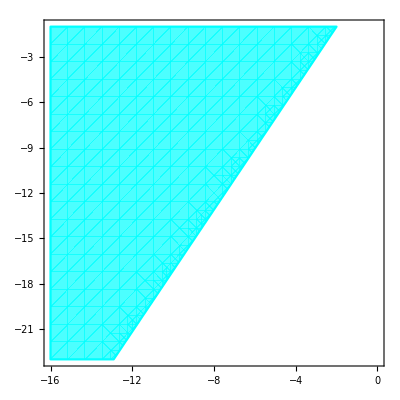
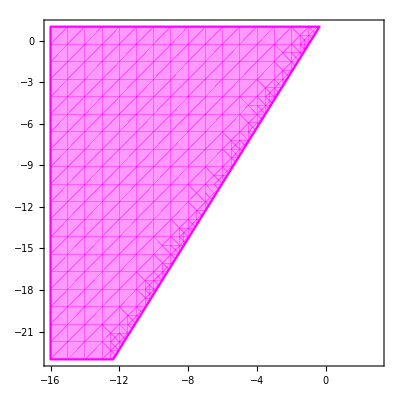
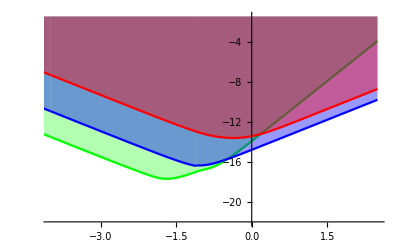
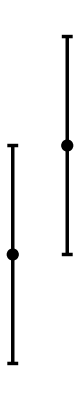
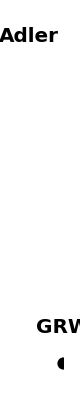
Show[-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],edcsl,-Graphics-,-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}]]

```mathematica
plotLIGO=Show[xrays,massprp,cantilever,edcsl,Plotgrav,Adler,grw,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (s^-1)"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed]
```

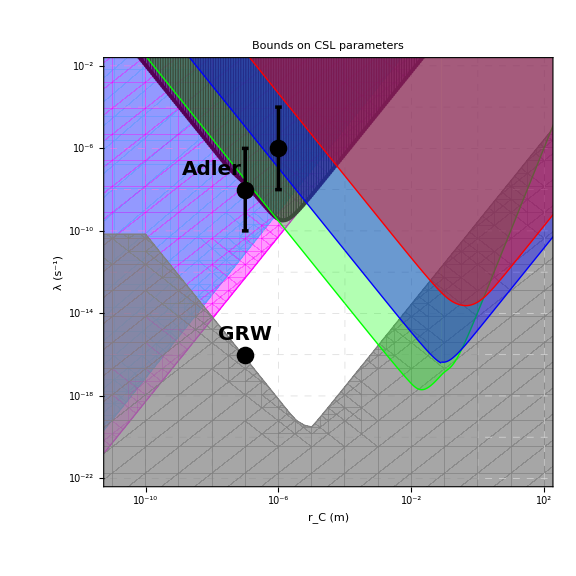
```mathematica
-Graphics-
Export["plotLIRRRR.png",plotLIGO]
```

-Graphics-

plotLIRRRR.png

```mathematica
plot1=Show[edcsl,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gtype: Symbol is not a type of graphics.

Show[edcsl,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

Show::gcomb: Could not combine the graphics objects in ….

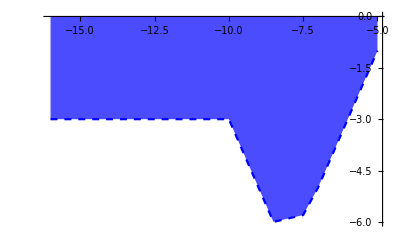
Show[edcsl,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot2=Show[edcsl,interferometry,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

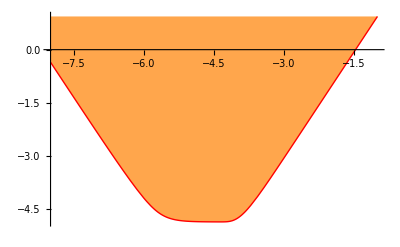
Show[edcsl,-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot3=Show[edcsl,interferometry,diamond,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

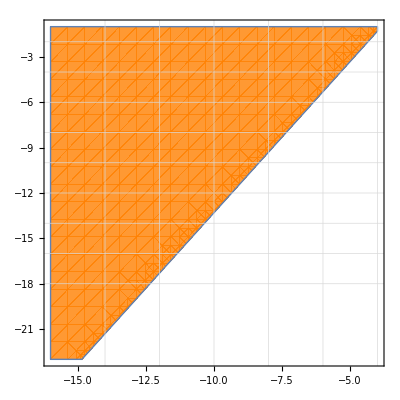
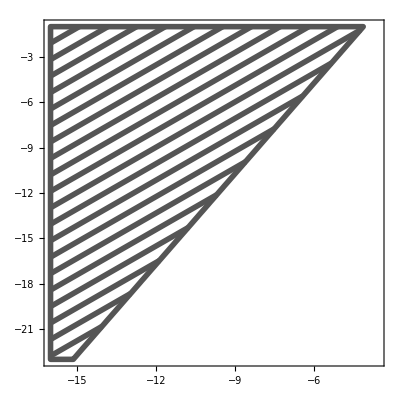
Show[edcsl,-Graphics-,-Graphics-,-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot4=Show[edcsl,kascsl6735Reg,pearle,interferometry,diamond,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

```mathematica
plot5=Show[edcsl,kascsl6735Reg,pearle,cantilever,interferometry,diamond,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[edcsl,-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot6=Show[edcsl,xrays,kascsl6735Reg,pearle,cantilever,interferometry,diamond,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[edcsl,-Graphics-,-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

Show::gcomb: Could not combine the graphics objects in ….

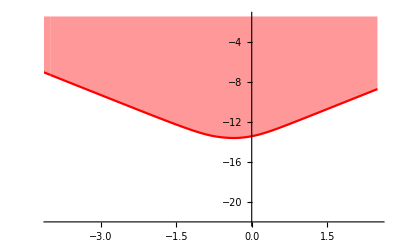
Show[edcsl,-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot7=Show[edcsl,xrays,kascsl6735Reg,pearle,PlotA,cantilever,interferometry,diamond,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

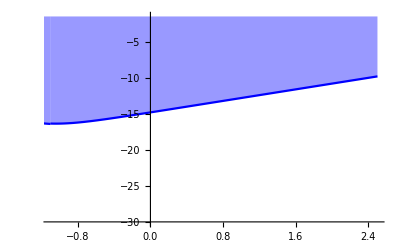
Show[edcsl,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot8=Show[edcsl,xrays,kascsl6735Reg,pearle,PlotLIG,PlotA,cantilever,interferometry,diamond,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

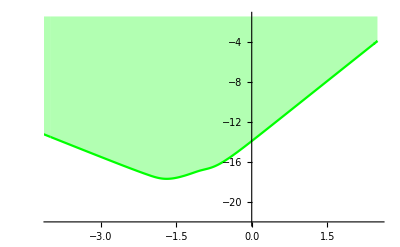
Show[edcsl,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot9=Show[edcsl,xrays,kascsl6735Reg,pearle,PlotLIS,PlotLIG,PlotA,cantilever,interferometry,diamond,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

```mathematica
Export["~/PlotCSL/plot1.pdf",plot1]
Export["~/PlotCSL/plot2.pdf",plot2]
Export["~/PlotCSL/plot3.pdf",plot3]
Export["~/PlotCSL/plot4.pdf",plot4]
Export["~/PlotCSL/plot5.pdf",plot5]
Export["~/PlotCSL/plot6.pdf",plot6]
Export["~/PlotCSL/plot7.pdf",plot7]
Export["~/PlotCSL/plot8.pdf",plot8]
Export["~/PlotCSL/plot9.pdf",plot9]
```

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot1.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot2.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot3.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot4.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot5.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot6.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot7.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot8.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot9.pdf.

$Failed

```mathematica
plot10=Show[edcsl,xrays,cantilever,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[edcsl,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot11=Show[edcsl,xrays,cantilever,PlotA,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[edcsl,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot12=Show[edcsl,xrays,cantilever,PlotLIG,PlotA,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[edcsl,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
plot13=Show[edcsl,xrays,cantilever,PlotLIS,PlotLIG,PlotA,PlotRange->range,PlotLabel->"Bounds on CSL parameters",LabelStyle->{Black,18},ImageSize->Large,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) (m)","λ (\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},FrameTicks->{{myTicksY,None},{myTicksX,None}},GridLines->{xset,yset},GridLinesStyle->Dashed,ImageResolution->100]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[edcsl,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},PlotRange→{{-1,-16},{-12,0}},Filling→Top,FillingStyle→RGBColor[0.33333333333333337, 0, 0.33333333333333337]],-Graphics-,-Graphics-,-Graphics-,PlotRange→{{-11,2},{-22,-2}},PlotLabel→Bounds on CSL parameters,LabelStyle→{GrayLevel[0],18},ImageSize→Large,FrameLabel→{r_C (m),λ (s^-1)},FrameTicks→{{{{-38,10^-38},{-34,10^-34},{-30,10^-30},{-26,10^-26},{-22,10^-22},{-20,10^-20},{-18,10^-18},{-16,10^-16},{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None},{{{-14,10^-14},{-12,10^-12},{-10,10^-10},{-8,10^-8},{-6,10^-6},{-4,10^-4},{-2,10^-2},{0,10^0},{2,10^2}},None}},GridLines→{{-14,-12,-10,-8,-6,-4,-2,0,2},{-38,-34,-30,-26,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2}},GridLinesStyle→Dashing[{Small,Small}],ImageResolution→100]

```mathematica
Export["~/PlotCSL/plot10.pdf",plot10]
Export["~/PlotCSL/plot11.pdf",plot11]
Export["~/PlotCSL/plot12.pdf",plot12]
Export["~/PlotCSL/plot13.pdf",plot13]
```

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot10.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot11.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot12.pdf.

$Failed

Export::nodir: Directory /home/andreas/PlotCSL/ does not exist.

Export::noopen: Cannot open ~/PlotCSL/plot13.pdf.

$Failed